Example 7

# A tree of Wavelet Decompositions

For a set of dilation matrices this demo illustrates nested spaces build by scaling functions of de la Vallée Poussin type.

Author: 		Ronny Bergmann
Created: 		17.08.2013
Last Changed: 	17.08.2013

#### License

This file is part of MPAWL.
  
      MPAWL is free software : you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.
  
      MPAWL is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.
  
      You should have received a copy of the GNU General Public License
    along with the MPAWL. If not, see <http://www.gnu.org/licenses/>.

### Loading the Library

The MPAWL is located in the parent directory (see MPAWL.m) in order to load the library, we add its path to $Path.

```mathematica
$Path = Join[$Path,{ParentDirectory[NotebookDirectory[]]}];
SetDirectory[NotebookDirectory[]];(*Set to actual directory*)
Needs["MPAWL`"];
```

Examine different ways to decompose a given sampling of a function by using different factorizations of the initial matrix. This Example is a new possibility of the de la Vallée Poussin means and hence extends the Dirichlet case is these observations by taking Shear matrices. The examples are taken from chapter 4 in [1] and more details to the wavelet transform and its complexity can be found in [2].

### Sampling

We take the function

```mathematica
f[x_] := Which[Abs[x]≤ 1,(x+1)^2(x-1)^2,True,0]
```

```mathematica
sf[x_] :=f[8/7x/π]
```

Which has a discontinuity in its second derivative at

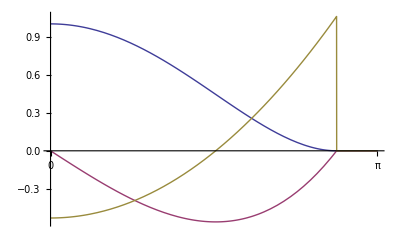

```mathematica
Plot[{sf[x],sf'[x],sf''[x]},{x,0,π}, Ticks-> {{0,π},Automatic},PlotRange->All]
```

Hence defining a radial function based on that, we obtain a circle (with radius 7 π/8, where orthogonal to each tangent we obtain a discontinuity in the directional derivative, i.e. we use

```mathematica
fr[x_] := sf[Norm[x]]
```

```mathematica
Plot3D[fr[{x,y}],{x,-π,π},{y,-π,π}]
```

-Graphics3D-

We now perform the same steps as in Example 6, but include one further Debug info to print just the images of the last level.

```mathematica
?decomposeData2D
```

decomposeData2D[g(Vec), JSet(Vec), mM, data]
decomposeData2D[l,g,JSet, mM, data, ckφM]

Decompose the data given as coefficients with respect to ckφφ this
method decomposes the data on different dialtionPaths given by JSet(Vec),
where the corresponding de la Vallee Poussin means (and wavelets) are given by
g(Vec) (see delaValleePoussinMean for restrictions on g). The dilation matrices
are given in terms of the characters used by dilationMatrix2D.

Both g and JSet might be given as vectors. If both are vectors, gVec has to be
one element longer than JSetVec. If one is given as a vector, the other is
expanded to a vector of corresponding length, having constant entries. This
length determines the number of levels of the wavelet decomposition, while g
also specifies additionally the starting space of mM.

If none of them is a vector, the second definition is needed to specify a level
depth of decomposition.

StyleBox["Options",FontWeight→"Bold"]

ImagePrefix → StyleBox["“Img”",
FontSlant→"Italic"] | String
	prefix that is used to save the images; the path in terms of the matrices
	is appended. This String may also contain Folders, that are relative to the
	Notebook.
ImageSuffix → StyleBox["“.png”",
FontSlant→"Italic"] | String
	suffix to determine the file format of the images.
DataPrefix → StyleBox["“Data”",
FontSlant→"Italic"] | String
	prefix that is used to save the data files; here an S or a W for the two
	subspaces is added and the decomposition path in terms of the matrices is
	appended. This String may also contain Folders, that are relative to the
	Notebook.

    Setting any of those String to an empty String disables the Image or Coefficient
	savings.

PlotResolution → StyleBox["64",
FontSlant→"Italic"] | nonnegative Integer
	resolution of the resulting Image generated by discreteFourierSeries
computeWavelet ->  → StyleBox["True",
FontSlant→"Italic"] | False
	whether to compute the wavelet part of the specific level and produce it's image
computeScale → StyleBox["False",
FontSlant→"Italic"] | True
	whether to compute the scale part of the specific level and produce it's image
Validate → StyleBox["True",
FontSlant→"Italic"] | False
	whether to perform a check (via isMatrixValid[mM]) on the matrix mM and mJ(s)
	Validity of data. If some matrices mN in the decomposition are not valid,
	the algorithm continues on the other leaves.
Debug → StyleBox["“None”",
FontSlant→"Italic"] | “Text” | “Time” | “Image”  | “Leaves“
	or any combination of these Words in one String (i.e. concatenated via “&”)
	to produce intermediate results, indicate progress and display computation
	times. The Term „Leaves“  restricts all debug output to just the last level.

and any Option of discretePlotFourierSeries (including Plot and BarLegend), that
are passed on and any Option of Export (especially Resolution but not ImageSize)
Show (especially ImageSize). By the last two, Fonts are scaled, but a pixel size
of the image is not that easy to be computed.

```mathematica
mM = 256*IdentityMatrix[2];
```

```mathematica
{ckφM,φMBS} = delaValleePoussinMean[1/10,mM,Debug-> "Text&Time", File-> {"example7/dlVP-ckS.dat","example7/dlVP-BS.dat"}, BracketSums-> True];
```

Loading de la Vallée Poussin mean from file “example7/dlVP-ckS.dat”...

failed.

Computing de la Vallée Poussin coefficients...

Creating the de La Vallée Poussin kernel took 9.16372 seconds.

Orthonormalization...

Orthonormalization took 80.16002 seconds.

Loading Bracket sums from file “example7/dlVP-BS.dat”...

failed. Computing Bracket sums to obtain the basis transform coefficients...

Computing the Bracket Sums took 41.81445 seconds.

```mathematica
data = sampleFunction[mM,fr, Debug-> "Text&Time", File-> "example7/samples.dat", validateMatrix-> False];
```

Loading data from file “example7/samples.dat”...

failed. Proceed with sampling...

Sampling the function...

Sampling took 13.75533 seconds.

Saving data to file “example7/samples.dat”.

```mathematica
cdata = changeBasis[mM,N[data], φMBS,Debug-> "Text&Time",Input-> "Time"];
```

The Fourier transform of the input took 0.05975 seconds.

The change of basis took 0.03633 seconds.

```mathematica
AbsoluteTiming[decomposeData2D[1/14,{{"Y","Y-"},{"Y","Y-"},{"X"}},mM,cdata,ImagePrefix->"",ImageSuffix->"",DataPrefix-> "example7/dlVP-",Debug->"Text&Time&Image&Leaves", ColorLegend-> False]][[1]]
```

Computing the decomposition. Only Debug output of the leaves of the wavelet tree are printed.

Decompose (256 | 0
0 | 256)  with X

Decompose (128 | 0
0 | 256) (X)  with X

Decompose (64 | 0
0 | 256) (XX)  with Y

Loading subspace coefficients from “example7/dlVP-XXY-S.dat” and “example7/dlVP-XXY-W.dat”...

Performing the Wavelet transform...

Performing the Wavelet transform took 7.5643 seconds.

Padding Data...

Fourier transforming...

Shifting back...

Creating Color Image...

The range of Values is from -3.77309×10^-5 to 3.59854×10^-5.

-Graphics-

Decompose (128 | 0
0 | 256) (X)  with X+

Decompose (64 | 0
-64 | 256) (XX+)  with Y

Loading subspace coefficients from “example7/dlVP-XX+Y-S.dat” and “example7/dlVP-XX+Y-W.dat”...

failed. Compute from scratch.

Computing the scaling function coefficients...

Scaling function coefficients computed in 29.56071 seconds.

Computing the wavelet function coefficients...

Wavelet function coefficients computed in 2.12927 seconds.

Orthonormalizing coefficients...

Orthonormalization took 7.03722 seconds.

Orthonormalizing coefficients...

Orthonormalization took 7.38232 seconds.

Performing the Wavelet transform...

Performing the Wavelet transform took 7.65533 seconds.

Padding Data...

Fourier transforming...

Shifting back...

Creating Color Image...

The range of Values is from -3.75763×10^-5 to 3.60189×10^-5.

-Graphics-

Decompose (256 | 0
0 | 256)  with X+

$Aborted

### Literature

[1] R: Bergmann, Translationsinvariante Räume multivariater anisotroper Funktionen auf dem Torus, Dissertation, University of Lübeck, 2013.

[2] R.Bergmann, The fast Fourier transform and fast wavelet transform for patterns on the torus, Appl. Comp. Harmon. Anal. 35 (2013) 39–51, doi: 10.1016/j.acha .2012 .07 .007.